# Illustration of the Kernel trick

## Generate random data

```mathematica
SeedRandom[12];
p1s=RandomVariate[NormalDistribution[0,1/4],{50,2}];
p2s=RandomVariate[NormalDistribution[0,1/4],{50,2}];
p3s=RandomVariate[NormalDistribution[0,1/4],{50,2}];
p4s=RandomVariate[NormalDistribution[0,1/4],{50,2}];
p1s=Table[p1s[[i]]+{1,1},{i,Length[p1s]}];
p2s=Table[p2s[[i]]+{1,-1},{i,Length[p2s]}];
p3s=Table[p3s[[i]]+{-1,-1},{i,Length[p3s]}];
p4s=Table[p4s[[i]]+{-1,1},{i,Length[p4s]}];
p1s=Join[p1s,p3s];
p2s=Join[p2s,p4s];
```

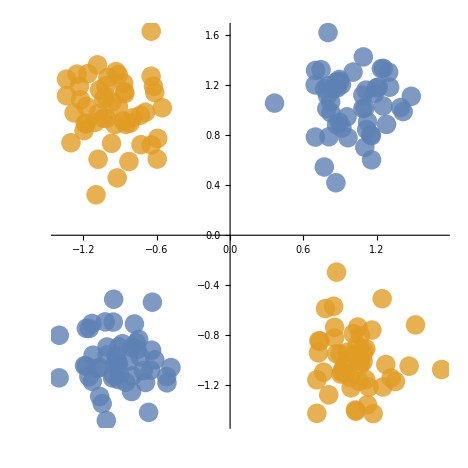

```mathematica
pts2d=ListPlot[{p1s,p2s},Axes->True,Ticks->True,PlotRange->All,PlotStyle->Directive[PointSize[0.03],Opacity[0.8]],AspectRatio->1]
```

## Lift to 3D using a homogeneous polynomial as a kernel

```mathematica
p13D={x1^2,x2^2,Sqrt[2]x1 x2}/.Table[{x1->p1s[[i,1]],x2->p1s[[i,2]]},{i,Length[p1s]}];
p23D={x1^2,x2^2,Sqrt[2]x1 x2}/.Table[{x1->p2s[[i,1]],x2->p2s[[i,2]]},{i,Length[p2s]}];
pts3d=ListPointPlot3D[{p13D,p23D},Ticks->False,BoxRatios->{1,1,1},PlotStyle->Directive[PointSize[0.03],Opacity[0.8]],PlotRange->All]
```

-Graphics3D-

## Find support vectors

```mathematica
minzp1=Sort[p13D,#1[[3]]<#2[[3]]&][[1,3]];
minzp2=Sort[p23D,#1[[3]]<#2[[3]]&][[-1,3]];
middle=1/2(minzp1+minzp2);
planes=Plot3D[{minzp2,minzp1,middle},{x,0,3},{y,0,3},PlotStyle->{Opacity[0.3]},Mesh->None,BoxRatios->{1,1,2},PlotRange->All];
```

```mathematica
Show[pts3d,planes]
```

-Graphics3D-

## Project back to 2D

### Decision boundary lines

```mathematica
bounds=Plot[{minzp1/(Sqrt[2]x),minzp2/(Sqrt[2]x),middle/(Sqrt[2]x)},{x,-3,3},PlotRange->{{-2,2},{-2,2}},AspectRatio->1];
```

### Coordinate axes

```mathematica
xAxis=ContourPlot[{x==0},{x,-3,3},{y,-3,3},ColorFunction->(Black&),PlotRange->{{-2,2},{-2,2}},AspectRatio->1,Frame->False];
yAxis=ContourPlot[{y==0},{x,-3,3},{y,-3,3},ColorFunction->(Black&),PlotRange->{{-2,2},{-2,2}},AspectRatio->1,Frame->False];
```

### Points

```mathematica
pts2d2=ListPlot[{p1s,p2s},Axes->True,Ticks->False,PlotRange->All,PlotStyle->Directive[PointSize[0.024],Opacity[0.8]],AspectRatio->1];
```

### Decision boundary region

```mathematica
rb=RegionPlot[Sqrt[2]x y≤minzp1&&Sqrt[2]x y≥minzp2,{x,-3,3},{y,-3,3},Mesh->None,PlotPoints->100,BoundaryStyle->None,PlotStyle->{Opacity[0.3],ColorData[97,"ColorList"][[3]]},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,Frame->False];
```

### Circle support vectors

```mathematica
suppvecs=Show[Graphics[Style[Circle[{-0.6356989971478506,-0.5361080845675568},0.07],Black,Thick]],Graphics[Style[Circle[{0.865509141972054,0.4200678998064338},0.07],Black,Thick]],Graphics[Style[Circle[{0.8707303823788733,-0.29561394578336864},0.07],Black,Thick]]];
```

### Plot all together

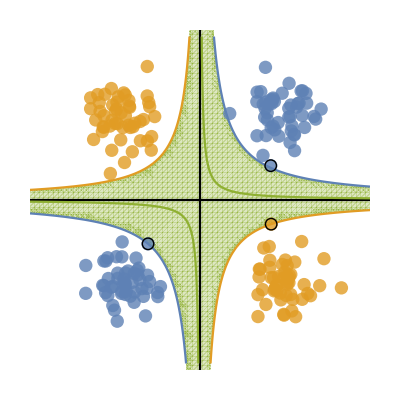

```mathematica
Show[rb,xAxis,yAxis,pts2d2,bounds,suppvecs]
```